```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/ninel/Documents/potts/potts

```mathematica
res0=Partition[<<"output.txt",3];
```

```mathematica
res={res0[[#,1]],res0[[#,2]]~Join~res0[[#,3]]}&/@Range[Length@res0];
```

```mathematica
(*desired = {2100,0.66,1.7,6.4};
dd=              {1000.0, 0.11,0.8,2.4};*)
(*desired = {1400,0.8,4.0,2.8};
dd=              {800.0, 0.09,2.1,1.6};*)
desired = {2500,0.84,1.9,1.7,5.3,2100,0.66,1.7,1.7,6.4};
dd=              {1000.0, 0.09,1.0,0.8,1.5,1000.0, 0.11,0.8, 0.6,2.4};
(*desired = {1400,0.8,4.0,3.0,2.8,1300,0.63,2.5,2.2,4.8};
dd=              {800.0, 0.09,2.1,1.4,1.6,800.0, 0.12,1.8,1.4,2.5};*)
(*desired = {1000,0.79,2.5,3.3};
dd=              {400.0, 0.11,1.4,1.3};*)
(*desired = {900,0.7,2.4,4.0};
dd=              {300.0, 0.1,1.2,1.3};*)
```

```mathematica
params={1,2,3,4,5};
```

```mathematica
w={5,1,1,0,0.5,5,1,1,0,0.5}
```

{5,1,1,0,0.5,5,1,1,0,0.5}

```mathematica
res[[-1,2]]
```

{574.293,0.761642,2.25312,2.01467,2.83984,589.05,0.598648,2.79152,2.30509,3.06977}

```mathematica
list=SortBy[{Map[#&,res[[;;,1,2;;]]],Map[#&,res[[;;,2]]],Map[Norm[(#-desired)/dd w]&,res[[;;,2]]]}ᵀ,First]
```

{{{3001},{574.293,0.761642,2.25312,2.01467,2.83984,589.05,0.598648,2.79152,2.30509,3.06977},12.4094},{{3001},{574.293,0.761642,2.25312,2.01467,2.83984,589.05,0.598648,2.79152,2.30509,3.06977},12.4094},{{3001},{574.747,0.743639,2.26096,2.00522,2.89503,596.004,0.592955,2.86285,2.30164,3.09659},12.4134},{{3001},{576.305,0.745602,2.24601,2.01162,2.84587,591.804,0.580416,2.86119,2.33067,3.19202},12.4237},{{3001},{576.413,0.742564,2.32164,2.07157,2.88046,581.16,0.588876,2.85467,2.32872,3.07904},12.4562},{{3001},{577.066,0.748286,2.37105,2.07021,2.93705,592.728,0.589008,2.85798,2.32517,3.17282},12.413},{{3001},{577.979,0.749529,2.3002,2.04847,2.85524,601.625,0.601065,2.83365,2.29746,3.13919},12.3723},{{3001},{579.564,0.755197,2.35162,2.07531,2.87283,601.214,0.597409,2.8415,2.29664,3.20471},12.3657},{{3001},{579.717,0.752054,2.29359,2.04488,2.87947,591.071,0.597183,2.85963,2.31751,3.07222},12.4007},{{3001},{579.971,0.751677,2.27156,2.02855,3.00189,585.426,0.596733,2.8661,2.33832,3.061},12.4153}}

```mathematica
list[[;;,2,1]]
```

{2432.51,2485.1,2518.52,2521.48,2530.73,2532.29}

```mathematica
ToPlot[x_]:={list[[;;,1,1]],Map[(x[[1]]-#)/(x[[1]]-Mean[x[[-3;;]]])&,x]}ᵀ
```

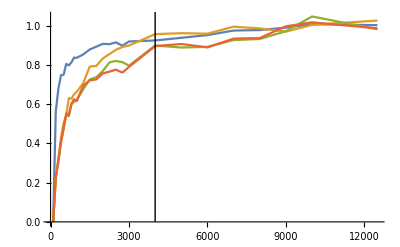

```mathematica
ListLinePlot[Map[ToPlot,list[[;;,2,{1,2,3,4}]]ᵀ],Epilog->{Line[{{4000,0},{4000,1.5}}]}]
```

```mathematica
{Mean[#],StandardDeviation[#]}&/@(list[[;;,2]]ᵀ)ᵀ
```

{{577.035,0.751183,2.29229,2.03852,2.88475,591.913,0.594094,2.84206,2.31463,3.11571},{2.21833,0.00674442,0.0438053,0.0272005,0.0507345,6.43844,0.00631632,0.0284341,0.0152961,0.0561466}}

{{2510.43,24.3821},{0.853525,0.0135146},{1.87675,0.099866},{1.68705,0.080998},{5.80698,0.300612},{2127.66,21.4296},{0.668469,0.0211399},{1.80621,0.114719},{1.56622,0.0736075},{8.05943,0.373464}}

{{70.25,0.77,183.644,930.372,32.906,470.196,630.78,2.54},{31.266,0.05,42.7027,171.059,16.7588,78.4803,191.399,1.36795}}

{{71.204,0.886,206.768,891.452,34.562,411.6,1012.68,2.242},{28.7506,0.0604979,42.0012,221.438,13.6237,91.1817,197.709,1.45229}}

```mathematica
list=SortBy[{Map[#-res[[-1,1]]&,res[[;;,1]]],Map[(#-desired)/dd^2&,res[[;;,2,params]]],Map[Norm[(#-desired)/desired w]&,res[[;;,2,params]]]}ᵀ,Last][[;;10]]
```

{{{0,32.05,-0.31,-66.09,248.21,1.81,152.27,594.19,-1.89},{0.0000820625,3.87807,0.0402178,-0.112085},0.0742864},{{0,-0.27,-0.28,7.51,19.54,-20.66,86.36,401.39,-0.43},{-0.000194766,3.19988,-0.0745761,0.00455166},0.0824196},{{0,17.14,-0.27,-42.32,-31.04,-15.25,-12.79,458.16,-0.85},{2.38281×10^-6,-3.95631,0.126823,0.219807},0.12933},{{0,31.83,-0.34,-60.04,148.9,-10.61,7.65,292.11,-0.83},{-0.000280055,-6.67121,0.109414,0.0519648},0.141364},{{0,6.,-0.42,-88.16,102.71,-9.89,65.43,476.49,-1.95},{-0.00083532,0.329063,0.115423,-0.0542406},0.162079},{{0,6.76,-0.36,-68.67,244.68,-21.4,165.33,-102.51,-0.75},{-0.0000533594,-7.39117,-0.123164,0.2786},0.165232},{{0,32.12,-0.39,-80.68,35.28,-24.66,27.27,105.51,0.33},{-0.000629422,-8.64778,-0.00500518,0.117395},0.16913},{{0,42.01,-0.34,-81.61,147.31,4.44,259.62,186.32,-0.08},{0.000507922,0.38377,-0.188903,0.0955849},0.170797},{{0,-4.38,-0.33,-57.84,-5.78,-16.72,229.52,225.53,-1.93},{0.0000809922,1.6468,-0.219649,0.067137},0.175369},{{0,-2.09,-0.17,-76.,66.62,-14.7,-3.4,363.68,-1.79},{0.000764852,2.00324,-0.141767,0.373426},0.193426}}

```mathematica
init=Position[list[[;;,1]],{0.,0.,0.,0.,0.,0.,0.}][[1,1]];
```

```mathematica
list[[;;init]]
```

{{{0.,-1.36,0.29,36.98,-888.14,0.901,-41.59},{0.0000551875,2.43258,0.163397,0.290053},0.153297},{{0.,0.,0.,0.,0.,0.,0.},{-0.000214477,5.69811,0.30904,0.0813692},0.190317}}

```mathematica
FirstNZ[x_]:=Module[{c=Map[If[#==0.,0,1]&,x],p},p=Position[c,1];If[p=={},0,x[[p[[1,1]]]]]]
```

```mathematica
Map[FirstNZ,list[[;;init]][[;;,1]]ᵀ]
```

{0,-1.36,0.29,36.98,-888.14,0.901,-41.59}

```mathematica
Renormalize[x_]:=x[[2;;]]
```

```mathematica
ch=res[[-1,1]]+Map[FirstNZ,list[[;;init]][[;;,1]]ᵀ]
```

{1.,5.74,1.08,61.77,1831.74,30.058,243.34}

```mathematica
Renormalize[ch]
```

{5.74,1.08,61.77,1831.74,30.058,243.34}